```mathematica
(*ClearAll["Global`*"]*)
path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP3D/COP3D/";
betas = {0.01,0.2,0.5};
data = Table[Import[path <> ToString[StringForm["cop3D``.txt", StringTrim@ToString@PaddedForm[betas[[i]],{2,2}]]],{"Table"}],{i,Range[3]}];
```

```mathematica
(*lsquared=50*50;
iterationsReported = 500;
m=Manipulate[
ListPlot[
Select[Take[data[[beta*10]],{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1],
{i,0,iterationsReported,1,AnimationRate->50},{beta,0.1,0.9,0.1}]*)
```

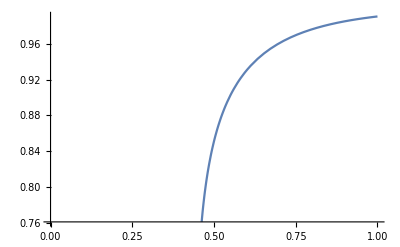

{0.0743315,0.925668,0.851337}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{beta→-0.441379},{beta→0.441379}}

```mathematica
mf[beta_] := (1-Csch[2*beta*1]^2)^(1/8);
Plot[mf[beta],{beta,0,1}]
{(1-mf[0.5])/2,(1+mf[0.5])/2,mf[0.5]}
Solve[(1-Csch[2*beta*1]^2)^(1/8)==0.5,beta]
```

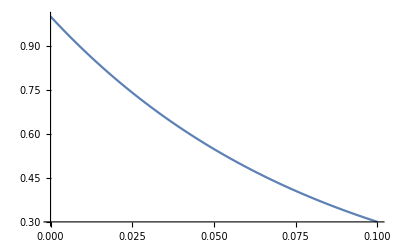

```mathematica
Plot[Exp[-beta*12],{beta,0,0.1}]
```

```mathematica
(*Table[path <> ToString[StringForm["cop``.txt", b]],{b,0.1,0.9,0.1}]*)
```

```mathematica
(*lsquared=50*50;
iterationsReported = 500;
m2[beta_]:=Manipulate[
ListPlot[
Select[Take[data[[beta*10]],{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1],
{i,0,iterationsReported,1,AnimationRate->50}]
path ="/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/";
m2frames=Flatten@Table[m2[m1],{n1,0,iterationsReported,1},{m1,0.1,0.9,0.1}];
Export[path<> ToString[StringForm["COP_at_``.gif", 0.6]],frames]
(*Export[path<> ToString[StringForm["COP_at_``.gif", #]],m2[#]]&/@Range[0.1,0.9,0.1]*)*)
```

```mathematica
(*frames=Flatten@Table[Manipulate[ContourPlot[q1/Norm[{x,y}-p[[1]]]+q2/Norm[{x,y}-p[[2]]],{x,-2,2},{y,-2,2},Contours->20,PlotRangePadding->0,Frame->False,PlotPoints->40,ImageSize->230,ColorFunction->"DarkRainbow"],{{q1,n1},-3,3},{{q2,m1},-3,3},{{p,{{-1,0},{1,0}}},{-1,-1},{1,1},Locator},Deployed->True,FrameMargins->0],{n1,-3,3},{m1,-3,3}];
Export["~/Desktop/frames.gif",frames];*)
```

```mathematica
l=50;
lsquared=l*l*l;
iterationsReported = 250/5;
myFrames=Flatten@
Table[Manipulate[
ListPointPlot3D[
Select[Take[data[[j]],{i*lsquared+1,(i+1)*lsquared}],#[[4]]==1&][[All,{1,2,3}]],PlotRange->{{0,l},{0,l},{0,l}},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1,ViewAngle->0.45, ViewPoint->{1.3, -2.4, 2.}, ImageSize->Medium,PlotLabel -> Style[StringForm["β = ``, iteration = ``",betas[[j]],i],15]],
{{i,n1},0,iterationsReported,1,AnimationRate->5},{{j,m1},Range[3],Slider},Deployed->True,FrameMargins->0],{m1,Range[3]},{n1,0,iterationsReported,1}];
path ="/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP3D/";
Export[path<>"cop3D250instepsof5round.gif",myFrames];
```

```mathematica
(*l=50;
lsquared=l*l*l;
iterationsReported = 250/5;
Manipulate[
ListPointPlot3D[
Select[Take[data[[2]],{i*lsquared+1,(i+1)*lsquared}],#[[4]]==1&][[All,{1,2,3}]],PlotRange->{{0,l},{0,l},{0,l}},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1, PlotLabel -> Style[StringForm["β = ``, iteration = ``",betas[[3]],i],15],ViewAngle->0.45, ViewPoint->{1.3, -2.4, 2.} ,ImageSize->Medium],
{{i,50},0,iterationsReported,1}]*)
```

```mathematica
(*path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP3D/COP3D/";
singleData = Import[path <> "cop3D0.20.txt",{"Table"}];*)
```

```mathematica
(*l=50;
ListPointPlot3D[
Select[singleData,#[[4]]==1&][[All,{1,2,3}]],PlotRange->{{0,l},{0,l},{0,l}},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1,ViewAngle->0.45, ViewPoint->{1.3, -2.4, 2.},ImageSize->Medium]*)
```